```mathematica
Table[{i,j},{i,1,3},{j,1,3}]//MatrixForm
Table[{3-j+1,3-i+1},{i,1,3},{j,1,3}]//MatrixForm
Table[{3-i+1,3-j+1},{i,1,3},{j,1,3}]//MatrixForm
```

((1
1) | (1
2) | (1
3)
(2
1) | (2
2) | (2
3)
(3
1) | (3
2) | (3
3))

((3
3) | (2
3) | (1
3)
(3
2) | (2
2) | (1
2)
(3
1) | (2
1) | (1
1))

((3
3) | (3
2) | (3
1)
(2
3) | (2
2) | (2
1)
(1
3) | (1
2) | (1
1))

```mathematica
Table[{i,j},{i,0,3},{j,0,3}]//MatrixForm
Table[{3-j,3-i},{i,0,3},{j,0,3}]//MatrixForm
Transpose[Table[{i,j},{i,0,3},{j,0,3}]]//MatrixForm
```

((0
0) | (0
1) | (0
2) | (0
3)
(1
0) | (1
1) | (1
2) | (1
3)
(2
0) | (2
1) | (2
2) | (2
3)
(3
0) | (3
1) | (3
2) | (3
3))

((3
3) | (2
3) | (1
3) | (0
3)
(3
2) | (2
2) | (1
2) | (0
2)
(3
1) | (2
1) | (1
1) | (0
1)
(3
0) | (2
0) | (1
0) | (0
0))

((0
0) | (1
0) | (2
0) | (3
0)
(0
1) | (1
1) | (2
1) | (3
1)
(0
2) | (1
2) | (2
2) | (3
2)
(0
3) | (1
3) | (2
3) | (3
3))

```mathematica
Map[{First[#],First[Last[#]]}&,{{{0,0},{3,3}},
{{1,1},{2,2}},
{{2,0},{3,1}},
{{1,0},{3,2}},
{{0,1},{2,3}},
{{0,2},{1,3}}}]
```

{{{0,0},3},{{1,1},2},{{2,0},3},{{1,0},3},{{0,1},2},{{0,2},1}}

```mathematica
InterpolatingPolynomial[%,{i,j}]
```

3-j

```mathematica
Map[{First[#],Last[Last[#]]}&,{{{0,0},{3,3}},
{{1,1},{2,2}},
{{2,0},{3,1}},
{{1,0},{3,2}},
{{0,1},{2,3}},
{{0,2},{1,3}}}]
InterpolatingPolynomial[%,{i,j}]
```

{{{0,0},3},{{1,1},2},{{2,0},1},{{1,0},2},{{0,1},3},{{0,2},3}}

3-i

```mathematica
a[i,j]:i,j∈[0..n]              (regular)
a[n-j,n-i]:i,j∈[0..n] (flipped)

cross symmetric: a[i,j]==a[n-j,n-i]
```

```mathematica
Flatten[Table[{i,j},{j,2,5},{i,1,j-1}],1]
```

{{1,2},{1,3},{2,3},{1,4},{2,4},{3,4},{1,5},{2,5},{3,5},{4,5}}

```mathematica
andd[f_,s_,e_]:=Block[{pos=s},While[(pos≤e)&&(f[pos]),pos++];If[pos≤e,False,True]]
```

```mathematica
anddd[f_,mx_]:=Block[{x=1,y=2},While[(y≤mx)&&f[x,y],If[x==y-1,x=1;y++,x++]];(x==1)&&(y==mx+1)]
```

```mathematica
anddd[{{True,True,True},{True,True,True},{True,True,True}}[[#1,#2]]&,3]
```

True

```mathematica
mx=5;
ls={};
Block[{x=1,y=2},While[(x<mx)&&(y≤mx),AppendTo[ls,{x,y}];If[x==y-1,x=1;y++,x++]]]
ls
```

```mathematica
cxsym[mat_]:=Block[{len=Length[mat]},anddd[mat[[#1,#2]]==mat[[len-#2+1,len-#1+1]]&,len]]
```

```mathematica
cxsym[mat_]:=Block[{len=Length[mat]},And@@And@@@Table[mat[[i,j]]==mat[[len-j+1,len-i+1]],{j,1,len},{i,1,len}]]
```

```mathematica
{cxsym[({{1, 0, 0}, {1, 0, 0}, {0, 1, 1}})],cxsym[({{1, 0, 0}, {1, 0, 0}, {0, 0, 1}})]}
```

{True,False}

```mathematica
cxsym2[mat_,len_]:=And@@And@@@Table[mat[[i,j]]==mat[[len-j+1,len-i+1]],{j,1,len},{i,1,len}]
```

```mathematica
cg6=Append[Permutations[Range[6]],{1,2,3,4,5,6}];
cg6len=GroupOrder[SymmetricGroup[6]]
```

720

```mathematica
ps=9;
```

```mathematica
Clear[ps]
```

```mathematica
pmat[perm_,n_]:=Block[{nums=Permute[Range[n],perm]},SparseArray[Table[{i,nums[[i]]}->1,{i,1,n}]]]
pmat[cg6[[1]],6]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1)

```mathematica
AdjacencyMatrix[nthor[EdgeList[CompleteGraph[6]],EdgeCount[CompleteGraph[6]],10]];

Map[ArrayPlot,DeleteDuplicates[Table[AdjacencyMatrix[Graph[perm[EdgeList[AdjacencyGraph[%]],cg6[[ps]]]]],{ps,1,720}]]]
```

{-Graphics-}

```mathematica
perm[elist_,p_]:=Map[p[[#[[1]]]]->p[[#[[2]]]]&,elist]
```

```mathematica
IsomorphicGraphQ[Graph[perm[EdgeList[CompleteGraph[6]],cg6[[1]]]],Graph[perm[EdgeList[CompleteGraph[6]],cg6[[2]]]]]
```

True

```mathematica
cxsyms62[AdjacencyGraph[({{0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1}})]]
```

{True,154}

```mathematica
¬cxsym2[pmat[cg6[[1]],6].({{0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1}}),6]
```

True

```mathematica
cxsyms62[nthor[EdgeList[CycleGraph[6]],EdgeCount[CycleGraph[6]],4]]
```

{True,324}

```mathematica
cxsyms6[g_]:=Block[{pos=1,elist=EdgeList[g],len=EdgeCount[g]},
While[¬cxsym2[AdjacencyMatrix[Graph[perm[elist,cg6[[pos]]]]]]&&(pos≤cg6len),pos++];pos≤cg6len]
```

```mathematica
cxsyms62[g_]:=Block[{pos=1,elist=EdgeList[g],len=EdgeCount[g],amat=AdjacencyMatrix[g]},
While[¬cxsym2[pmat[cg6[[pos]],6].amat,6]&&(pos≤cg6len),pos++];pos<cg6len]
```

```mathematica
cxsyms[g_]:=Block[{pos=1,elist=EdgeList[g],len=EdgeCount[g],amat=AdjacencyMatrix[g]},
While[¬cxsym2[pmat[cg6[[pos]],len].amat,len]&&(pos≤cg6len),pos++];pos≤cg6len]
```

```mathematica
cxsymsaux[g_,len_]:=Block[{pos=1,elist=EdgeList[g],amat=AdjacencyMatrix[g]},
While[¬cxsym2[pmat[cg6[[pos]],len].amat,len]&&(pos≤cg6len),pos++];pos≤cg6len]
findxsym[g_]:=Block[{elist=EdgeList[g],len=EdgeCount[g],pos=0,mx=2^EdgeCount[g]},While[(pos<mx)&&!(csymsaux[nthor[elist,len,pos],len]&&(GroupOrder[GraphAutomorphismGroup[nthor[elist,len,pos]]]>1)),pos++];If[pos==mx,{False,nthor[elist,len,pos],pos},True]]
```

```mathematica
findxsym[CompleteGraph[3]]
```

True

```mathematica
ags=Select[GraphData[6;;7],(VertexConnectivity[GraphData[#]]>1)&&(!MemberQ[VertexDegree[GraphData[#]],2])&];
Length[%]
```

168

```mathematica
GraphData[{6,149},"Planar"]
```

False

```mathematica
Position[IdentityMatrix[3],1]
```

{{1,1},{2,2},{3,3}}

```mathematica
Mod[i,2]
```

```mathematica
Position[({{0, 0, 1}, {0, 1, 0}, {1, 0, 0}}),1]
```

{{1,3},{2,2},{3,1}}

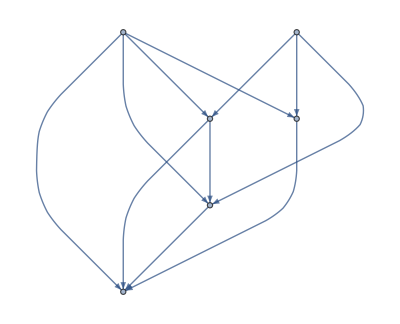
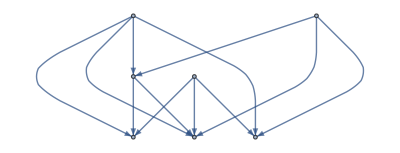
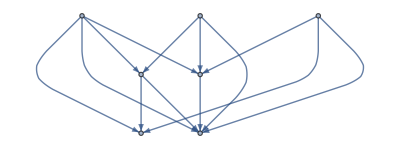
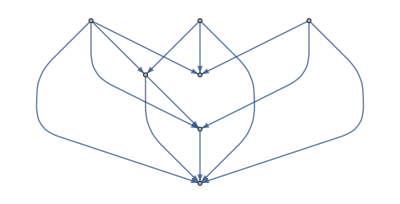
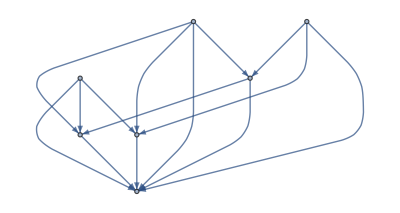
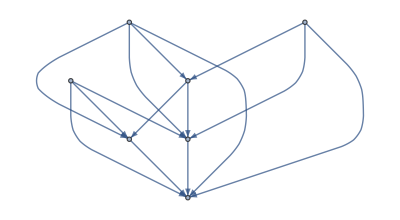
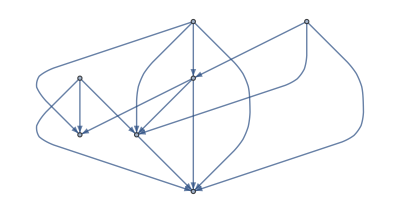
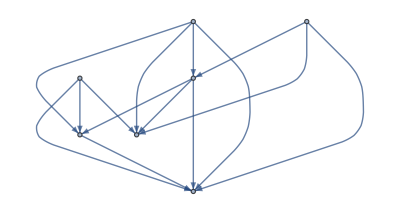
{{{6,114},True},{{6,130},True},{{6,148},True},{{6,149},{False,-Graphics-,2048}},{{7,344},True},{{7,550},True},{{7,551},True},{{7,552},True},{{7,553},True},{{7,737},True},{{7,738},True},{{7,740},True},{{7,763},True},{{7,764},True},{{7,765},True},{{7,766},True},{{7,767},True},{{7,768},True},{{7,770},True},{{7,771},True},{{7,772},True},{{7,773},True},{{7,839},{False,-Graphics-,4096}},{{7,840},{False,-Graphics-,8192}},{{7,841},{False,-Graphics-,8192}},{{7,842},{False,-Graphics-,16384}},{{7,843},{False,-Graphics-,16384}},{{7,844},{False,-Graphics-,16384}},{{7,845},{False,-Graphics-,16384}},{{7,846},{False,-Graphics-,32768}},{{7,847},{False,-Graphics-,65536}},{{7,888},True},{{7,889},True},{{7,890},True},{{7,892},True},{{7,893},True},{{7,894},True},{{7,895},True},{{7,896},True},{{7,897},True},{{7,898},True},{{7,899},True},{{7,901},True},{{7,902},True},{{7,903},True},{{7,904},True},{{7,905},True},{{7,906},True},{{7,907},True},{{7,910},True},{{7,912},True},{{7,914},True},{{7,915},True},{{7,934},{False,-Graphics-,4096}},{{7,935},{False,-Graphics-,8192}},{{7,949},{False,-Graphics-,8192}},{{7,952},{False,-Graphics-,8192}},{{7,953},{False,-Graphics-,16384}},{{7,954},True},{{7,955},True},{{7,956},{False,-Graphics-,4096}},{{7,963},{False,-Graphics-,4096}},{{7,964},{False,-Graphics-,8192}},{{7,965},{False,-Graphics-,16384}},{{7,967},{False,-Graphics-,16384}},{{7,968},{False,-Graphics-,32768}},{{7,986},{False,-Graphics-,16384}},{{7,987},{False,-Graphics-,16384}},{{7,988},{False,-Graphics-,32768}},{{7,989},{False,-Graphics-,65536}},{{7,990},True},{{7,991},True},{{7,992},True},{{7,993},True},{{7,1001},{False,-Graphics-,65536}},{{7,1002},{False,-Graphics-,32768}},{{7,1003},{False,-Graphics-,32768}},{{7,1004},{False,-Graphics-,32768}},{{7,1005},{False,-Graphics-,65536}},{{7,1006},{False,-Graphics-,131072}},{{7,1007},True},{{7,1008},{False,-Graphics-,16384}},{{7,1009},{False,-Graphics-,16384}},{{7,1013},{False,-Graphics-,32768}},{{7,1015},True},{{7,1017},{False,-Graphics-,8192}},{{7,1018},{False,-Graphics-,8192}},{{7,1019},{False,-Graphics-,16384}},{{7,1020},True},{{7,1023},{False,-Graphics-,65536}},{{7,1025},{False,-Graphics-,32768}},{{7,1026},{False,-Graphics-,32768}},{{7,1027},{False,-Graphics-,65536}},{{7,1028},{False,-Graphics-,131072}},{{7,1029},True},{{7,1030},{False,-Graphics-,65536}},{{7,1031},True},{{7,1032},True},{{7,1033},True},{{7,1034},{False,-Graphics-,131072}},{{7,1035},True},{{7,1037},True},{{7,1038},True},{{7,1039},True},{{7,1040},True},{{Apollonian,2},True},{{BiggestLittlePolygon,6},True},{{Circulant,{7,{1,2}}},True},{{Complete,6},True},{{Complete,7},True},{{CompleteBipartite,{3,4}},True},{{CompleteTripartite,{1,3,3}},True},{{Cone,{3,3}},True},{{Cone,{3,4}},True},{{Cone,{4,3}},True},{{Fan,{2,4}},True},{{Fan,{2,5}},True},{{Fan,{3,3}},True},{{Fan,{3,4}},True},{{Fan,{4,3}},True},{{Harary,{3,7}},True},{{Heptahedral,2},{False,-Graphics-,2048}},{{Heptahedral,4},{False,-Graphics-,8192}},{{Heptahedral,5},True},{{Heptahedral,6},True},{{Heptahedral,7},True},{{Heptahedral,8},True},{{Heptahedral,9},True},{{Heptahedral,10},{False,-Graphics-,8192}},{{Heptahedral,11},{False,-Graphics-,8192}},{{Heptahedral,12},{False,-Graphics-,8192}},{{Heptahedral,13},{False,-Graphics-,16384}},{{Heptahedral,15},True},{{Heptahedral,16},{False,-Graphics-,16384}},{{Heptahedral,18},{False,-Graphics-,4096}},{{Heptahedral,20},{False,-Graphics-,8192}},{{Heptahedral,21},{False,-Graphics-,4096}},{{Heptahedral,22},{False,-Graphics-,8192}},{{Heptahedral,23},{False,-Graphics-,16384}},{{Heptahedral,25},True},{{Heptahedral,26},{False,-Graphics-,8192}},{{Heptahedral,27},True},{{Heptahedral,28},{False,-Graphics-,16384}},{{Heptahedral,29},{False,-Graphics-,32768}},{{Heptahedral,30},{False,-Graphics-,8192}},{{Heptahedral,31},{False,-Graphics-,16384}},{{Heptahedral,34},True},{{Hexahedral,3},{False,-Graphics-,1024}},{{Hexahedral,4},{False,-Graphics-,2048}},{{Hexahedral,5},{False,-Graphics-,4096}},{{JohnsonSkeleton,13},True},{{JohnsonSkeleton,49},{False,-Graphics-,8192}},{{King,{2,3}},True},{MoserSpindle,{False,-Graphics-,2048}},{OctahedralGraph,True},{{Prism,3},True},{{Quartic,{7,1}},True},{{Queen,{2,3}},True},{SelfDualGraph1,True},{SelfDualGraph2,{False,-Graphics-,4096}},{SelfDualGraph3,True},{{TorusGrid,{3,4}},True},{{Turan,{6,5}},True},{{Turan,{7,4}},True},{{Turan,{7,6}},True},{UtilityGraph,True},{{Wheel,6},True},{{Wheel,7},True}}

{{{6,114},True},{{6,130},True},{{6,148},True},{{6,149},{False,-Graphics-,2048}},{{7,344},True},{{7,550},True},{{7,551},True},{{7,552},True},{{7,553},True},{{7,737},True},{{7,738},True},{{7,740},True},{{7,763},True},{{7,764},True},{{7,765},True},{{7,766},True},{{7,767},True},{{7,768},True},{{7,770},True},{{7,771},True},{{7,772},True},{{7,773},True},{{7,839},{False,-Graphics-,4096}},{{7,840},{False,-Graphics-,8192}},{{7,841},{False,-Graphics-,8192}},{{7,842},{False,-Graphics-,16384}},{{7,843},{False,-Graphics-,16384}},{{7,844},{False,-Graphics-,16384}},{{7,845},{False,-Graphics-,16384}},{{7,846},{False,-Graphics-,32768}},{{7,847},{False,-Graphics-,65536}},{{7,888},True},{{7,889},True},{{7,890},True},{{7,892},True},{{7,893},True},{{7,894},True},{{7,895},True},{{7,896},True},{{7,897},True},{{7,898},True},{{7,899},True},{{7,901},True},{{7,902},True},{{7,903},True},{{7,904},True},{{7,905},True},{{7,906},True},{{7,907},True},{{7,910},True},{{7,912},True},{{7,914},True},{{7,915},True},{{7,934},{False,-Graphics-,4096}},{{7,935},{False,-Graphics-,8192}},{{7,949},{False,-Graphics-,8192}},{{7,952},{False,-Graphics-,8192}},{{7,953},{False,-Graphics-,16384}},{{7,954},True},{{7,955},True},{{7,956},{False,-Graphics-,4096}},{{7,963},{False,-Graphics-,4096}},{{7,964},{False,-Graphics-,8192}},{{7,965},{False,-Graphics-,16384}},{{7,967},{False,-Graphics-,16384}},{{7,968},{False,-Graphics-,32768}},{{7,986},{False,-Graphics-,16384}},{{7,987},{False,-Graphics-,16384}},{{7,988},{False,-Graphics-,32768}},{{7,989},{False,-Graphics-,65536}},{{7,990},True},{{7,991},True},{{7,992},True},{{7,993},True},{{7,1001},{False,-Graphics-,65536}},{{7,1002},{False,-Graphics-,32768}},{{7,1003},{False,-Graphics-,32768}},{{7,1004},{False,-Graphics-,32768}},{{7,1005},{False,-Graphics-,65536}},{{7,1006},{False,-Graphics-,131072}},{{7,1007},True},{{7,1008},{False,-Graphics-,16384}},{{7,1009},{False,-Graphics-,16384}},{{7,1013},{False,-Graphics-,32768}},{{7,1015},True},{{7,1017},{False,-Graphics-,8192}},{{7,1018},{False,-Graphics-,8192}},{{7,1019},{False,-Graphics-,16384}},{{7,1020},True},{{7,1023},{False,-Graphics-,65536}},{{7,1025},{False,-Graphics-,32768}},{{7,1026},{False,-Graphics-,32768}},{{7,1027},{False,-Graphics-,65536}},{{7,1028},{False,-Graphics-,131072}},{{7,1029},True},{{7,1030},{False,-Graphics-,65536}},{{7,1031},True},{{7,1032},True},{{7,1033},True},{{7,1034},{False,-Graphics-,131072}},{{7,1035},True},{{7,1037},True},{{7,1038},True},{{7,1039},True},{{7,1040},True},{{Apollonian,2},True},{{BiggestLittlePolygon,6},True},{{Circulant,{7,{1,2}}},True},{{Complete,6},True},{{Complete,7},True},{{CompleteBipartite,{3,4}},True},{{CompleteTripartite,{1,3,3}},True},{{Cone,{3,3}},True},{{Cone,{3,4}},True},{{Cone,{4,3}},True},{{Fan,{2,4}},True},{{Fan,{2,5}},True},{{Fan,{3,3}},True},{{Fan,{3,4}},True},{{Fan,{4,3}},True},{{Harary,{3,7}},True},{{Heptahedral,2},{False,-Graphics-,2048}},{{Heptahedral,4},{False,-Graphics-,8192}},{{Heptahedral,5},True},{{Heptahedral,6},True},{{Heptahedral,7},True},{{Heptahedral,8},True},{{Heptahedral,9},True},{{Heptahedral,10},{False,-Graphics-,8192}},{{Heptahedral,11},{False,-Graphics-,8192}},{{Heptahedral,12},{False,-Graphics-,8192}},{{Heptahedral,13},{False,-Graphics-,16384}},{{Heptahedral,15},True},{{Heptahedral,16},{False,-Graphics-,16384}},{{Heptahedral,18},{False,-Graphics-,4096}},{{Heptahedral,20},{False,-Graphics-,8192}},{{Heptahedral,21},{False,-Graphics-,4096}},{{Heptahedral,22},{False,-Graphics-,8192}},{{Heptahedral,23},{False,-Graphics-,16384}},{{Heptahedral,25},True},{{Heptahedral,26},{False,-Graphics-,8192}},{{Heptahedral,27},True},{{Heptahedral,28},{False,-Graphics-,16384}},{{Heptahedral,29},{False,-Graphics-,32768}},{{Heptahedral,30},{False,-Graphics-,8192}},{{Heptahedral,31},{False,-Graphics-,16384}},{{Heptahedral,34},True},{{Hexahedral,3},{False,-Graphics-,1024}},{{Hexahedral,4},{False,-Graphics-,2048}},{{Hexahedral,5},{False,-Graphics-,4096}},{{JohnsonSkeleton,13},True},{{JohnsonSkeleton,49},{False,-Graphics-,8192}},{{King,{2,3}},True},{MoserSpindle,{False,-Graphics-,2048}},{OctahedralGraph,True},{{Prism,3},True},{{Quartic,{7,1}},True},{{Queen,{2,3}},True},{SelfDualGraph1,True},{SelfDualGraph2,{False,-Graphics-,4096}},{SelfDualGraph3,True},{{TorusGrid,{3,4}},True},{{Turan,{6,5}},True},{{Turan,{7,4}},True},{{Turan,{7,6}},True},{UtilityGraph,True},{{Wheel,6},True},{{Wheel,7},True}}

```mathematica
Monitor[Table[{ags[[o]],findxsym[GraphData[ags[[o]]]]},{o,1,Length[ags]}],o]
DeleteDuplicates[%]
```

```mathematica
nthor[EdgeList[CompleteGraph[6]],EdgeCount[CompleteGraph[6]],5]
syms[%]
```

-Graphics-

{True,False}

```mathematica
sym[g_]:=GroupOrder[GraphAutomorphismGroup[g]]≠1
```

```mathematica
syms[g_]:={sym[g],cxsyms6[g]}
syms2[g_]:={sym[g],cxsyms62[g]}
```

```mathematica
syms0[g_]:={sym[g],cxsym[g]}
```

```mathematica
nthor[elist_,len_,x_]:=Block[{v=PadLeft[IntegerDigits[x,2],len]},Graph[Table[Piecewise[{{elist[[i]][[1]]->elist[[i]][[2]], v[[i]]==0}, {elist[[i]][[2]]->elist[[i]][[1]], v[[i]]==1}}],{i,1,len}]]]
```

```mathematica
allsyms[g_]:=Block[{elist=EdgeList[g],len=EdgeCount[g]},Table[syms[nthor[elist,len,x]],{x,0,2^len-1}]]
allsyms2[g_]:=Block[{elist=EdgeList[g],len=EdgeCount[g]},Table[syms2[nthor[elist,len,x]],{x,0,2^len-1}]]
```

```mathematica
allsyms0[g_]:=Block[{elist=EdgeList[g],len=EdgeCount[g]},Table[syms0[nthor[elist,len,x]],{x,0,2^len-1}]]
```

```mathematica
DeleteDuplicates[allsyms[CompleteGraph[4]]]
```

{{False,True},{False,False},{True,False}}

```mathematica
DeleteDuplicates[allsyms[CompleteGraph[5]]]
```

{{False,True},{False,False},{True,False},{True,True}}

```mathematica
Monitor[DeleteDuplicates[allsyms0[CompleteGraph[6]]],x]
```

{{False,True},{True,True}}

```mathematica
Monitor[DeleteDuplicates[allsyms[CompleteGraph[6]]],x]
```

{{False,True},{True,True}}

```mathematica
Monitor[DeleteDuplicates[allsyms2[CycleGraph[6]]],x]
```

{{False,True},{True,True},{True,False}}

```mathematica
Monitor[DeleteDuplicates[allsyms2[CompleteGraph[6]]],x]
```

$Aborted

```mathematica
symcount[g_]:=Map[Boole,syms2[g]]
allsymscount[g_]:=Block[{elist=EdgeList[g],len=EdgeCount[g]},Sum[symcount[nthor[elist,len,x]],{x,0,2^len-1}]]
```

```mathematica
Monitor[allsymscount[GraphData[gs[[13]]]],x]
```

{64,42}

```mathematica
gs=Select[GraphData[3;;6],VertexConnectivity[GraphData[#]]>1&];
```

```mathematica
Length[gs]
```

70

```mathematica
Map[VertexCount[GraphData[#]]&,gs]
```

{5,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,5,6,6,5,6,4,6,6,6,5,6,6,5,6,6,6,6,5,5,5,6,6,5,6,6,6,4,4,3,6,6,6,5,6}

```mathematica
gs2=Select[gs,VertexCount[GraphData[#]]==6&]
```

{{6,76},{6,77},{6,80},{6,81},{6,82},{6,83},{6,86},{6,92},{6,95},{6,96},{6,108},{6,109},{6,110},{6,111},{6,112},{6,114},{6,124},{6,125},{6,128},{6,129},{6,130},{6,135},{6,136},{6,137},{6,138},{6,139},{6,140},{6,141},{6,144},{6,148},{6,149},{6,150},{BiggestLittlePolygon,6},{BlackBishop,{3,4}},{Complete,6},{CompleteBipartite,{2,4}},{Cone,{3,3}},{Cycle,6},DominoGraph,{Fan,{1,5}},{Fan,{2,4}},{Fan,{3,3}},{Fan,{4,2}},{HamiltonLaceable,{6,1}},{Hexahedral,3},{Hexahedral,4},{Hexahedral,5},{King,{2,3}},OctahedralGraph,{Polyiamond,{4,1}},{Prism,3},{Queen,{2,3}},{TriangularGrid,2},{Turan,{6,5}},UtilityGraph,{Wheel,6}}

```mathematica
Length[gs2]
```

56

```mathematica
gss2=ParallelTable[DeleteDuplicates[allsyms2[GraphData[gs2[[k]]]]],{k,1,56}];
```

```mathematica
Table[{GroupOrder[GraphAutomorphismGroup[GraphData[gs[[k]]]]],Length[gss[[k]]]},{k,1,70}]
```

{{4,2},{4,2},{4,2},{2,2},{2,2},{8,2},{8,2},{2,1},{1,1},{1,1},{2,1},{4,2},{2,2},{2,2},{4,2},{4,2},{12,2},{4,1},{4,2},{2,1},{2,1},{16,2},{8,1},{2,1},{2,1},{12,2},{4,1},{2,1},{2,1},{2,1},{12,2},{8,1},{12,2},{4,2},{2,2},{720,2},{12,2},{48,1},{36,2},{10,2},{12,2},{4,2},{4,2},{2,2},{4,2},{12,2},{12,2},{48,2},{2,1},{8,2},{2,1},{2,1},{4,1},{2,1},{4,1},{12,2},{16,2},{48,2},{120,2},{2,1},{12,2},{16,2},{8,2},{24,2},{6,2},{6,2},{48,2},{72,2},{8,2},{10,2}}

```mathematica
{{4,3},{4,2},{4,2},{2,2},{2,2},{8,2},{8,2},{2,1},{1,1},{1,1},{2,1},{4,2},{2,2},{2,2},{4,2},{4,2},{12,2},{4,1},{4,3},{2,1},{2,1},{16,4},{8,1},{2,1},{2,1},{12,2},{4,2},{2,1},{2,1},{2,1},{12,2},{8,1},{12,2},{4,2},{2,2},{720,4},{12,4},{48,2},{36,2},{10,4},{12,3},{4,4},{4,4},{2,2},{4,4},{12,2},{12,2},{48,2},{2,2},{8,2},{2,1},{2,1},{4,1},{2,1},{4,1},{12,4},{16,2},{48,4},{120,4},{2,2},{12,4},{16,4},{8,4},{24,3},{6,3},{6,2},{48,4},{72,2},{8,2},{10,2}}
```

```mathematica
0->{False,False};
1->{False,True};
2->{True,False};
3->{True,True};
```

```mathematica
(x⊻(!#[[1]]))&&(y⊻(!#[[2]]))
```

```mathematica
{Or@@Map[(x⊻(!#[[1]]))&&(y⊻(!#[[2]]))&,gss[[3]]],gss[[3]]}
```

{(x&&!y)||(!x&&!y),{{True,False},{False,False}}}

```mathematica
Table[{GroupOrder[GraphAutomorphismGroup[GraphData[gs[[k]]]]],Sort[Map[FromDigits[#,2]&,Map[Boole,gss[[k]],{2}]]]},{k,1,70}]//Column
```

{4,{0,1,2}}
{4,{0,2}}
{4,{0,2}}
{2,{0,2}}
{2,{0,2}}
{8,{0,2}}
{8,{0,2}}
{2,{0}}
{1,{0}}
{1,{0}}
{2,{0}}
{4,{0,2}}
{2,{0,2}}
{2,{0,2}}
{4,{0,2}}
{4,{0,2}}
{12,{0,2}}
{4,{0}}
{4,{0,1,2}}
{2,{0}}
{2,{0}}
{16,{0,1,2,3}}
{8,{0}}
{2,{0}}
{2,{0}}
{12,{0,2}}
{4,{0,1}}
{2,{0}}
{2,{0}}
{2,{0}}
{12,{0,2}}
{8,{0}}
{12,{0,2}}
{4,{0,2}}
{2,{0,2}}
{720,{0,1,2,3}}
{12,{0,1,2,3}}
{48,{2,3}}
{36,{0,2}}
{10,{0,1,2,3}}
{12,{0,2,3}}
{4,{0,1,2,3}}
{4,{0,1,2,3}}
{2,{0,2}}
{4,{0,1,2,3}}
{12,{0,2}}
{12,{0,2}}
{48,{0,2}}
{2,{0,1}}
{8,{0,2}}
{2,{0}}
{2,{0}}
{4,{0}}
{2,{0}}
{4,{0}}
{12,{0,1,2,3}}
{16,{0,2}}
{48,{0,1,2,3}}
{120,{0,1,2,3}}
{2,{0,1}}
{12,{0,1,2,3}}
{16,{0,1,2,3}}
{8,{0,1,2,3}}
{24,{0,1,2}}
{6,{0,1,3}}
{6,{0,2}}
{48,{0,1,2,3}}
{72,{0,2}}
{8,{0,2}}
{10,{0,2}}

```mathematica
(x⊻(!#[[1]]))&&(y⊻(!#[[2]]))&;
{Or@@Map[(x⊻(!#[[1]]))&&(y⊻(!#[[2]]))&,gss[[3]]],gss[[3]]}
```

{(x&&!y)||(!x&&!y),{{True,False},{False,False}}}

```mathematica
SortBy[Table[{GroupOrder[GraphAutomorphismGroup[GraphData[gs2[[k]]]]],BooleanMinimize[Or@@Map[(sy⊻(!#[[1]]))&&(xy⊻(!#[[2]]))&,gss[[k]]],"CNF"]},{k,1,56}],Reverse]//Column
```

{12,sy&&!xy}
{1,!sy&&!xy}
{1,!sy&&!xy}
{2,!sy&&!xy}
{2,!sy&&!xy}
{2,!sy&&!xy}
{2,!sy&&!xy}
{2,!sy&&!xy}
{2,!sy&&!xy}
{2,!sy&&!xy}
{4,!sy&&!xy}
{4,!sy&&!xy}
{6,!sy&&!xy}
{12,!sy&&!xy}
{12,!sy&&!xy}
{12,!sy&&!xy}
{12,!sy&&!xy}
{16,!sy&&!xy}
{16,!sy&&!xy}
{48,!sy&&!xy}
{48,!sy&&!xy}
{72,!sy&&!xy}
{2,!xy}
{2,!xy}
{2,!xy}
{2,!xy}
{2,!xy}
{2,!xy}
{2,!xy}
{2,!xy}
{2,!xy}
{2,!xy}
{2,!xy}
{4,!xy}
{4,!xy}
{4,!xy}
{4,!xy}
{4,!xy}
{4,!xy}
{4,!xy}
{4,!xy}
{4,!xy}
{4,!xy}
{8,!xy}
{8,!xy}
{8,!xy}
{8,!xy}
{8,!xy}
{10,!xy}
{12,!xy}
{12,!xy}
{16,!xy}
{36,!xy}
{48,!xy}
{48,!xy}
{720,!xy}

```mathematica
SortBy[Table[{GroupOrder[GraphAutomorphismGroup[GraphData[gs[[k]]]]],BooleanMinimize[BooleanMinimize[Or@@Map[(sy⊻(!#[[1]]))&&(xy⊻(!#[[2]]))&,gss[[k]]],"CNF"]⇒(sy⇒xy)]},{k,1,70}],First]
```

{{1,True},{1,True},{2,True},{2,True},{2,True},{2,True},{2,True},{2,True},{2,True},{2,True},{2,True},{2,True},{2,True},{2,True},{2,True},{2,True},{2,!sy||xy},{2,!sy||xy},{2,!sy||xy},{2,!sy||xy},{2,!sy||xy},{2,!sy||xy},{4,True},{4,True},{4,True},{4,True},{4,!sy||xy},{4,!sy||xy},{4,!sy||xy},{4,!sy||xy},{4,!sy||xy},{4,!sy||xy},{4,!sy||xy},{4,!sy||xy},{4,!sy||xy},{4,!sy||xy},{4,!sy||xy},{6,!sy||xy},{6,!sy||xy},{8,True},{8,True},{8,!sy||xy},{8,!sy||xy},{8,!sy||xy},{8,!sy||xy},{8,!sy||xy},{10,!sy||xy},{10,!sy||xy},{12,!sy||xy},{12,!sy||xy},{12,!sy||xy},{12,!sy||xy},{12,!sy||xy},{12,!sy||xy},{12,!sy||xy},{12,!sy||xy},{12,!sy||xy},{12,!sy||xy},{16,!sy||xy},{16,!sy||xy},{16,!sy||xy},{24,!sy||xy},{36,!sy||xy},{48,!sy||xy},{48,!sy||xy},{48,!sy||xy},{48,!sy||xy},{72,!sy||xy},{120,!sy||xy},{720,!sy||xy}}

```mathematica
"Below, if extensible, shows that cross symmetric implies standard symmetric, while above disproves the converse, i.e. that standard symmetric implies cross symmetric";
```

```mathematica
SortBy[Table[{GroupOrder[GraphAutomorphismGroup[GraphData[gs[[k]]]]],BooleanMinimize[BooleanMinimize[Or@@Map[(sy⊻(!#[[1]]))&&(xy⊻(!#[[2]]))&,gss2[[k]]],"CNF"]⇒(xy⇒sy)]},{k,1,56}],First]//Column
```

{1,sy||!xy}
{1,sy||!xy}
{2,sy||!xy}
{2,sy||!xy}
{2,sy||!xy}
{2,sy||!xy}
{2,sy||!xy}
{2,sy||!xy}
{2,sy||!xy}
{2,sy||!xy}
{2,sy||!xy}
{2,sy||!xy}
{2,sy||!xy}
{2,sy||!xy}
{2,sy||!xy}
{2,sy||!xy}
{2,sy||!xy}
{2,sy||!xy}
{2,sy||!xy}
{2,sy||!xy}
{2,sy||!xy}
{4,sy||!xy}
{4,sy||!xy}
{4,sy||!xy}
{4,sy||!xy}
{4,sy||!xy}
{4,sy||!xy}
{4,sy||!xy}
{4,sy||!xy}
{4,sy||!xy}
{4,sy||!xy}
{4,sy||!xy}
{4,sy||!xy}
{4,sy||!xy}
{4,sy||!xy}
{4,sy||!xy}
{8,sy||!xy}
{8,sy||!xy}
{8,sy||!xy}
{8,sy||!xy}
{8,sy||!xy}
{10,sy||!xy}
{12,True}
{12,True}
{12,sy||!xy}
{12,sy||!xy}
{12,sy||!xy}
{12,sy||!xy}
{12,sy||!xy}
{12,sy||!xy}
{12,sy||!xy}
{16,sy||!xy}
{36,sy||!xy}
{48,sy||!xy}
{48,sy||!xy}
{720,True}

```mathematica
BooleanConvert[!(xy&&!(su)),"IMPLIES"]
```

xy⇒su

```mathematica
"The above meaning that if there is a cross-symmetry then the undirected graph is symmetric (sofar)";
```

```mathematica
SortBy[Table[{GroupOrder[GraphAutomorphismGroup[GraphData[gs[[k]]]]],BooleanMinimize[(BooleanMinimize[Or@@Map[(sy⊻(!#[[1]]))&&(xy⊻(!#[[2]]))&,gss[[k]]],"CNF"])⇒(!(xy&&!(GroupOrder[GraphAutomorphismGroup[GraphData[gs[[k]]]]]>1))),"CNF"]},{k,1,70}],First]//Column
```

{1,True}
{1,True}
{2,True}
{2,True}
{2,True}
{2,True}
{2,True}
{2,True}
{2,True}
{2,True}
{2,True}
{2,True}
{2,True}
{2,True}
{2,True}
{2,True}
{2,True}
{2,True}
{2,True}
{2,True}
{2,True}
{2,True}
{4,True}
{4,True}
{4,True}
{4,True}
{4,True}
{4,True}
{4,True}
{4,True}
{4,True}
{4,True}
{4,True}
{4,True}
{4,True}
{4,True}
{4,True}
{6,True}
{6,True}
{8,True}
{8,True}
{8,True}
{8,True}
{8,True}
{8,True}
{8,True}
{10,True}
{10,True}
{12,True}
{12,True}
{12,True}
{12,True}
{12,True}
{12,True}
{12,True}
{12,True}
{12,True}
{12,True}
{16,True}
{16,True}
{16,True}
{24,True}
{36,True}
{48,True}
{48,True}
{48,True}
{48,True}
{72,True}
{120,True}
{720,True}

```mathematica
nthor[elist_,len_,x_]:=Block[{v=PadLeft[IntegerDigits[x,2],len]},Graph[Table[Piecewise[{{elist[[i]][[1]]->elist[[i]][[2]], v[[i]]==0}, {elist[[i]][[2]]->elist[[i]][[1]], v[[i]]==1}}],{i,1,len}]]]
```

```mathematica
eqpaths[g_]:=Block[{ps={},p,foundeq=False,vc=VertexCount[g]},
Do[p=Length[FindPath[g,i,j,∞,All]];If[MemberQ[ps,p]&&p≠0,foundeq=True;Break[],If[p≠0,AppendTo[ps,p],0]],{j,1,vc},{i,1,vc}];foundeq]
```

```mathematica
haseqor[g_]:=Block[{elist=EdgeList[g],len=EdgeCount[g],mx=2^EdgeCount[g]-1},
Last[Reap[Do[If[!eqpaths[nthor[elist,len,x]],Sow[x],0],{x,0,mx}]]]]
```

```mathematica
g=CompleteGraph[7];
ParallelSow[x_]:=Sow[x];
SetSharedFunction[ParallelSow];
elist=EdgeList[g];len=EdgeCount[g];mx=2^EdgeCount[g]-1;
Parallelize[Do[If[!eqpaths[nthor[elist,len,x]],Sow[x],0],{x,0,mx}]]//Reap//Last
```

{}

```mathematica
Clear[g,elist,len,mx]
```

```mathematica
ParallelSow[x_]:=Sow[x];
SetSharedFunction[ParallelSow];
ParallelHaseqor[g_]:=Module[{elist=EdgeList[g],len=EdgeCount[g],mx=2^EdgeCount[g]-1},Parallelize[
Do[If[!eqpaths[nthor[elist,len,x]],Sow[x],0],{x,0,mx}]]]//Reap//Last
```

```mathematica
ParallelHaseqor[CompleteGraph[5]]
```

{}

```mathematica
gs=Select[GraphData[4;;7],(VertexConnectivity[GraphData[#]]>1)&&(!MemberQ[VertexDegree[GraphData[#]],2])&];
Length[%]
```

172

```mathematica
Monitor[Table[ParallelHaseqor[GraphData[gs[[o]]]],{o,1,Length[gs]}],o]
```

{{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{}}

```mathematica
haseqor[CompleteGraph[3]]
```

{}

```mathematica
haseqor[CompleteGraph[4]]
```

{}

```mathematica
haseqor[CompleteGraph[5]]
```

{}

```mathematica
Monitor[haseqor[CompleteGraph[6]],x]
```

{}

```mathematica
neq[l_]:=Flatten[Table[l[[i]]≠l[[j]],{j,2,Length[l]},{i,1,j-1}]]
```

```mathematica
{neq[{Subscript[a, 0],Subscript[a, 1],Subscript[a, 2]}],
neq[{Subscript[b, 0],Subscript[b, 1],Subscript[b, 2]}],
neq[{Subscript[b, 0],Subscript[b, 1],Subscript[b, 2]}],
neq[{Subscript[d, 0],Subscript[d, 1],Subscript[d, 2]}],
Table[Subscript[a, i]≠Subscript[b, i],{i,0,2}],
Table[Subscript[a, i]≠Subscript[c, i],{i,0,2}],
Table[Subscript[a, i]≠Subscript[d, i],{i,0,1}],
Table[Subscript[b, i]≠Subscript[d, i],{i,0,2}],
Table[Subscript[c, i]≠Subscript[d, i],{i,0,2}],
Table[Subscript[b, i]==Subscript[c, i],{i,0,1}],
{Subscript[a, 2]==Subscript[d, 2]},
neq[{Subscript[a, 0],Subscript[a, 1],Subscript[c, 2]}],
neq[{Subscript[d, 0],Subscript[d, 1],Subscript[b, 2]}]}//Flatten
```

```mathematica
Reduce[{Subscript[a, 0]≠Subscript[a, 1],Subscript[a, 0]≠Subscript[a, 2],Subscript[a, 1]≠Subscript[a, 2],Subscript[b, 0]≠Subscript[b, 1],Subscript[b, 0]≠Subscript[b, 2],Subscript[b, 1]≠Subscript[b, 2],Subscript[b, 0]≠Subscript[b, 1],Subscript[b, 0]≠Subscript[b, 2],Subscript[b, 1]≠Subscript[b, 2],Subscript[d, 0]≠Subscript[d, 1],Subscript[d, 0]≠Subscript[d, 2],Subscript[d, 1]≠Subscript[d, 2],Subscript[a, 0]≠Subscript[b, 0],Subscript[a, 1]≠Subscript[b, 1],Subscript[a, 2]≠Subscript[b, 2],Subscript[a, 0]≠Subscript[c, 0],Subscript[a, 1]≠Subscript[c, 1],Subscript[a, 2]≠Subscript[c, 2],Subscript[a, 0]≠Subscript[d, 0],Subscript[a, 1]≠Subscript[d, 1],Subscript[b, 0]≠Subscript[d, 0],Subscript[b, 1]≠Subscript[d, 1],Subscript[b, 2]≠Subscript[d, 2],Subscript[c, 0]≠Subscript[d, 0],Subscript[c, 1]≠Subscript[d, 1],Subscript[c, 2]≠Subscript[d, 2],Subscript[b, 0]==Subscript[c, 0],Subscript[b, 1]==Subscript[c, 1],Subscript[a, 2]==Subscript[d, 2],Subscript[a, 0]≠Subscript[a, 1],Subscript[a, 0]≠Subscript[c, 2],Subscript[a, 1]≠Subscript[c, 2],Subscript[d, 0]≠Subscript[d, 1],Subscript[d, 0]≠Subscript[b, 2],Subscript[d, 1]≠Subscript[b, 2]},Integers]
```

$Aborted

```mathematica
SimpleGraph[Graph[{Subscript[a, 0]<->Subscript[a, 1],Subscript[a, 0]<->Subscript[a, 2],Subscript[a, 1]<->Subscript[a, 2],Subscript[b, 0]<->Subscript[b, 1],Subscript[b, 0]<->Subscript[b, 2],Subscript[b, 1]<->Subscript[b, 2],Subscript[b, 0]<->Subscript[b, 1],Subscript[b, 0]<->Subscript[b, 2],Subscript[b, 1]<->Subscript[b, 2],Subscript[d, 0]<->Subscript[d, 1],Subscript[d, 0]<->Subscript[d, 2],Subscript[d, 1]<->Subscript[d, 2],Subscript[a, 0]<->Subscript[b, 0],Subscript[a, 1]<->Subscript[b, 1],Subscript[a, 2]<->Subscript[b, 2],Subscript[a, 0]<->Subscript[c, 0],Subscript[a, 1]<->Subscript[c, 1],Subscript[a, 2]<->Subscript[c, 2],Subscript[a, 0]<->Subscript[d, 0],Subscript[a, 1]<->Subscript[d, 1],Subscript[b, 0]<->Subscript[d, 0],Subscript[b, 1]<->Subscript[d, 1],Subscript[b, 2]<->Subscript[d, 2],Subscript[c, 0]<->Subscript[d, 0],Subscript[c, 1]<->Subscript[d, 1],Subscript[c, 2]<->Subscript[d, 2],Subscript[a, 0]<->Subscript[a, 1],Subscript[a, 0]<->Subscript[c, 2],Subscript[a, 1]<->Subscript[c, 2],Subscript[d, 0]<->Subscript[d, 1],Subscript[d, 0]<->Subscript[b, 2],Subscript[d, 1]<->Subscript[b, 2]}]]
```

-Graphics-

```mathematica
FindPermutation[{1,2,3},{3,1,2}]
```

```mathematica
PermutationProduct[Cycles[{{1,2,3}}],Cycles[{{1,2,3}}],Cycles[{{1,2,3}}]]
```

Cycles[{}]

```mathematica
Map[Mod[-1-1#,7]&,Range[0,6]]
```

{6,5,4,3,2,1,0}

```mathematica
ps=Permutations[{1,2,3}];
Length[ps]

t[i_,j_]:=Block[{es={{1,3},{1,2},{2,3}},s1=ps[[i]],s2=ps[[j]]},
Block[{sd=Length[Complement[Map[{s1[[#[[2]]]],s2[[#[[1]]]]}&,es],es]]==0,ns=Length[Complement[Map[{s1[[#[[1]]]],s2[[#[[2]]]]}&,es],es]]==0},
{i,j,sd,ns}]]
Flatten[Table[t[i,j],{i,1,Length[ps]},{j,1,Length[ps]}],1]
Select[%,#[[3]]||#[[4]]&]
```

6

{{1,1,False,True},{1,2,False,False},{1,3,False,False},{1,4,False,False},{1,5,False,False},{1,6,False,False},{2,1,False,False},{2,2,False,False},{2,3,False,False},{2,4,False,False},{2,5,False,False},{2,6,False,False},{3,1,False,False},{3,2,False,False},{3,3,False,False},{3,4,False,False},{3,5,False,False},{3,6,False,False},{4,1,False,False},{4,2,False,False},{4,3,False,False},{4,4,False,False},{4,5,False,False},{4,6,False,False},{5,1,False,False},{5,2,False,False},{5,3,False,False},{5,4,False,False},{5,5,False,False},{5,6,False,False},{6,1,False,False},{6,2,False,False},{6,3,False,False},{6,4,False,False},{6,5,False,False},{6,6,True,False}}

{{1,1,False,True},{6,6,True,False}}

```mathematica
{ps[[1]],Map[{ps[[1]][[#[[1]]]],ps[[1]][[#[[2]]]]}&,{{1,3},{1,2},{2,3}}]}
```

{{1,2,3},{{1,3},{1,2},{2,3}}}

```mathematica
{ps[[6]],Map[{ps[[6]][[#[[2]]]],ps[[6]][[#[[1]]]]}&,{{1,3},{1,2},{2,3}}],Map[{ps[[6]][[#[[2]]]],ps[[6]][[#[[1]]]]}&,Map[Reverse,{{1,3},{1,2},{2,3}}]]}
```

{{3,2,1},{{1,3},{2,3},{1,2}},{{3,1},{3,2},{2,1}}}

```mathematica
ArcTan[1]
```

π/4

```mathematica
ArcTan[(1/2)/(√3/2)]
```

π/6

```mathematica
Abs[((√3)/2+ⅈ/2)]
```

1

```mathematica
"
P(a,b) : ∃e_f:(∄e:e_f→e)∧(∀e≠e_f,∃e':e→e')
F : P(a,b) → P(c,d)
```

```mathematica
Fc1[a,b]:={n-b,n-a}
Fc2[a,b]:={n-a,n-b}

Fc1[a,b]=={n-b,n-a}=={b,a}->{n/2,n/2}
Fc2[b,a]=={n-b,n-a}=={a,b}->{a+b==n}
```

```mathematica
({{0, 1, 0}, {0, 0, 1}, {1, 0, 0}})({{0, 1, 1}, {1, 0, 1}, {1, 1, 0}})
{0,0}->{2-0,2-0}=={2,2}
{1,1}->{2-1,2-1}=={1,1}
{2,0}->{2-0,2-2}=={2,0}
```

```mathematica
F[R[2,0]]==[2,0]

[a,b]->F[a,b]
P[a,b]->F[P][F[a,b]]
Want:=∃[a,b]:F[R[a,b]]==[a,b]
```

```mathematica
({{1, 2, 3}, {4, 5, 6}, {7, 8, 9}})[[1,2]]
```

2